# Msci Project Calculations

## Approaching from One-dimension:

## Taking α = 0 (i.e anisotropy turned off)

```mathematica
H1={{0,0,a+I b,L*(a+I b)},{0,0,-L (a+I b),-(a+I b)},{a-I b,-L (a-I b),0,0},{L(a-I b),-a+I b,0,0}};
MatrixForm[H1]
Eigenvalues[H1]
```

(0 | 0 | a+ⅈ b | (a+ⅈ b) L
0 | 0 | -((a+ⅈ b) L) | -a-ⅈ b
a-ⅈ b | -((a-ⅈ b) L) | 0 | 0
(a-ⅈ b) L | -a+ⅈ b | 0 | 0)

{-√(a^2+b^2) (-1+L),√(a^2+b^2) (-1+L),-√(a^2+b^2) (1+L),√(a^2+b^2) (1+L)}

## Rxy=0 is equivalent to Pure Kitaev (NO J) Rx>0 is equivalent to Kitaev-Heisenberg

```mathematica
Rxy=2;f[k_]:=2+2 Cos[k];E1[k_]:=Rxy*Sqrt[f[k]];E2[k_]:=(Rxy+1)*Sqrt[f[k]];
```

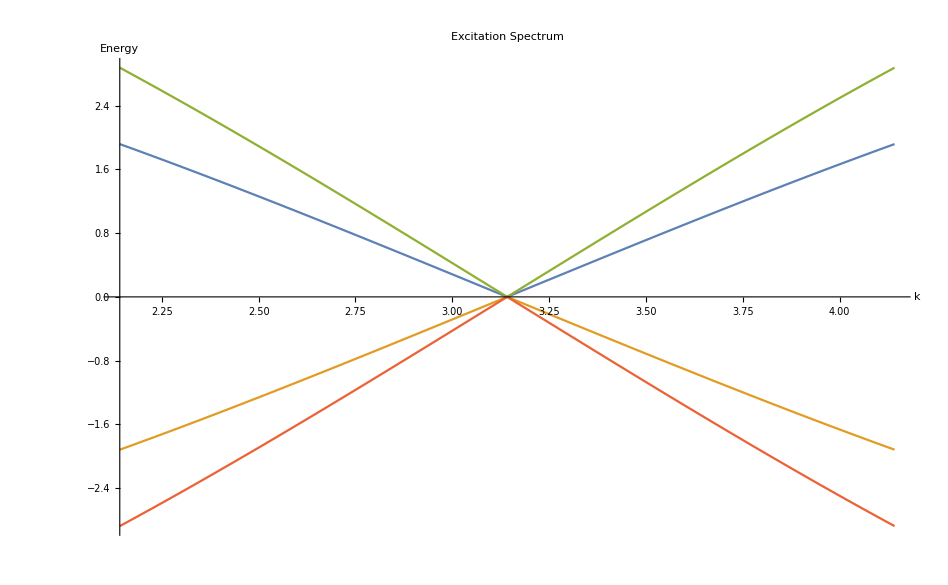

```mathematica
Plot[{E1[k],-E1[k],E2[k],-E2[k]},{k,Pi-1,Pi+1},PlotLabel-> Excitation Spectrum  ,AxesLabel->{k,Energy}]
```

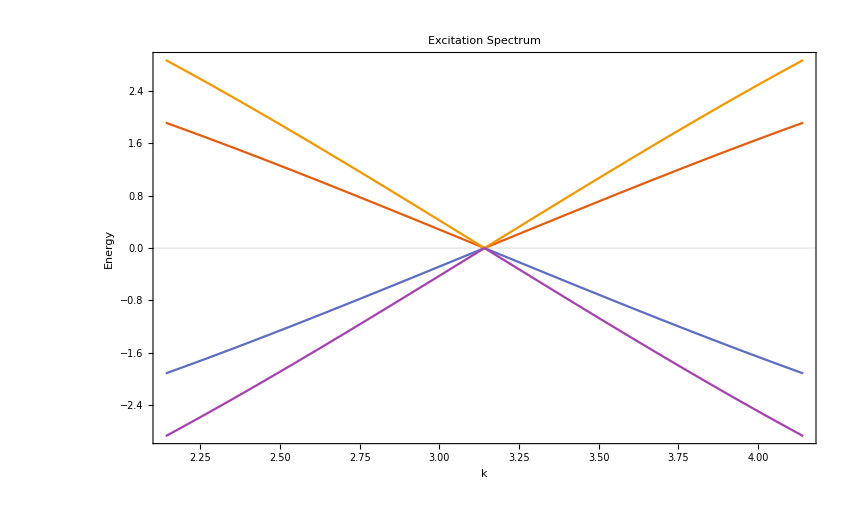

```mathematica
Plot[{E1[k],-E1[k],E2[k],-E2[k]},{k,π-1,π+1},PlotTheme->"Scientific",PlotLabel->Excitation Spectrum,AxesLabel->{k,Energy}]
```

```mathematica
Plot[{E1[k],-E1[k],E2[k],-E2[k]},{k,0,2 π},PlotTheme->"Scientific",PlotLabel->Excitation Spectrum,AxesLabel->{k,Energy}]
```

## Turning anisotropy on: α >0 & setting Jxy=0 (equivalent to saying Jz >> Jxy)

```mathematica
x=0.2;f[k_]:=2+2 Cos[k];
E1[k_]:=Sqrt[2(2+2 Cos[k])+x^2+4 Cos[k/2]Sqrt[2+2 Cos[k]+x^2]];
E2[k_]:=Sqrt[2(2+2 Cos[k])+x^2-4 Cos[k/2]Sqrt[2+2 Cos[k]+x^2]];
```

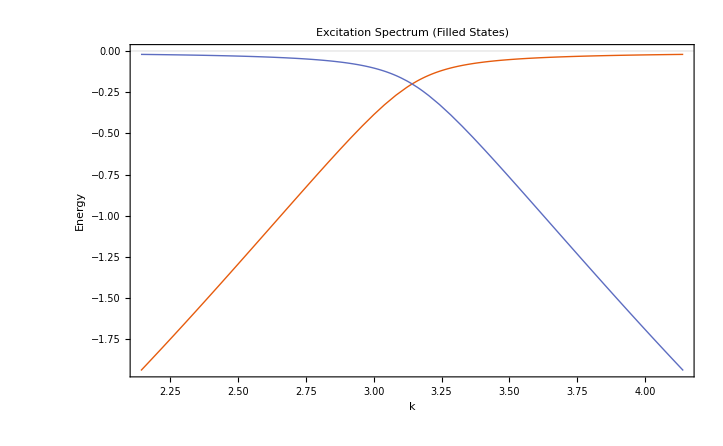

```mathematica
Plot[{-E1[k],-E2[k]},{k,π-1,π+1},PlotTheme->"Scientific",PlotLabel->Style["Excitation Spectrum (Filled States)"],PlotStyle->Thickness[Large],AxesLabel->{k,Energy}]
```

## Total Energy as a function of Magnetisation

```mathematica
Clear[x] #magnetisation;
Clear[R] #JzK;
f[k_]:=2+2 Cos[k];
e[x_,k_,R_]:=Sqrt[2f[k]+R^2 x^2+4 Cos[k/2]Sqrt[f[k]+R^2 x^2]];
G[x_,k_,R_]:=(2 R^2 x+(4 R^2 x Cos[k/2])/(√(2+R^2 x^2+2 Cos[k])))/(2 √(R^2 x^2+2 (2+2 Cos[k])+4 Cos[k/2] √(2+R^2 x^2+2 Cos[k])));
```

```mathematica
Clear[R0, r,m,M,M0]
mmax=3;msteps=200;
R=0.1; 
For[i=1,i<=msteps,i++,m=-mmax+2i mmax/msteps;magnetism1[i]=m;energy1[i]=R m^2- NIntegrate[e[m,k,R],{k,0,2 Pi}]/2Pi]
List1=Table[{magnetism1[i],energy1[i]-energy1[100]},{i,0,msteps}];
```

```mathematica
Clear[R,R0, r,m,M,M0]
R=0.2; 
For[i=1,i<=msteps,i++,m=-mmax+2i mmax/msteps;magnetism2[i]=m;energy2[i]=R m^2- NIntegrate[e[m,k,R],{k,0,2 Pi}]/2Pi]
List2=Table[{magnetism2[i],energy2[i]-energy2[100]},{i,0,msteps}];
```

```mathematica
Clear[R,R0, r,m,M,M0]
R=0.3; 
For[i=1,i<=msteps,i++,m=-mmax+2i mmax/msteps;magnetism3[i]=m;energy3[i]=R m^2- NIntegrate[e[m,k,R],{k,0,2 Pi}]/2Pi]
List3=Table[{magnetism3[i],energy3[i]-energy3[100]},{i,0,msteps}];
```

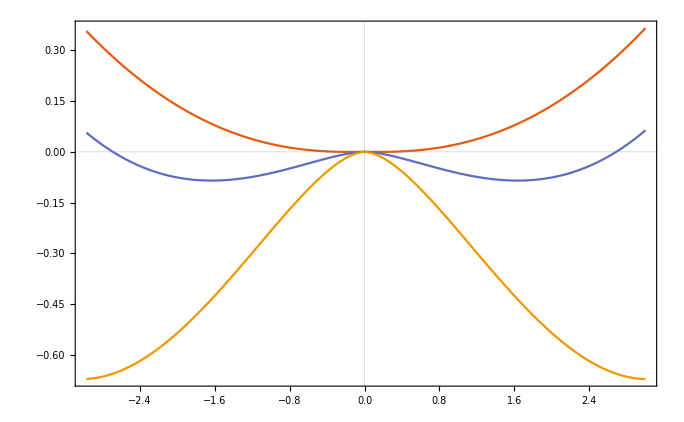

```mathematica
ListLinePlot[{List1,List2,List3},PlotTheme->"Scientific"]
```

## How does magnetisation (m) change with R?

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.1415}. NIntegrate obtained 0.00781999 and 1.30826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.1415}. NIntegrate obtained 0.00917875 and 1.04592×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.1415}. NIntegrate obtained 0.0124607 and 2.17997×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

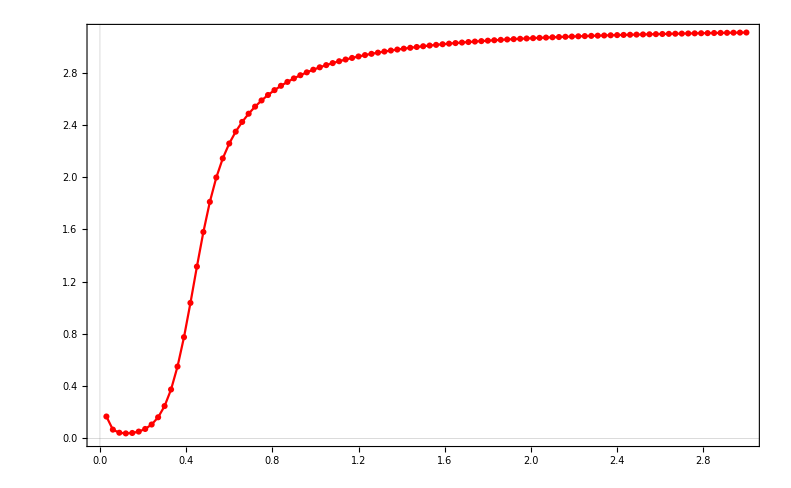

```mathematica
Clear[R0, r,m,M,M0]
rmax=1.5;rsteps=100;
R0={};
M0={};
M=1;
For[i=1,i<=rsteps,i++,r=2i rmax/rsteps;m=(1/(2r)) NIntegrate[G[M,k,r],{k,0,2 Pi}];M=m;AppendTo[R0,r];AppendTo[M0,m]];

ListLinePlot[Table[{R0[[i]],M0[[i]]}, {i,1,rsteps}],PlotTheme->"Scientific",PlotStyle->Red,PlotMarkers->Automatic]
```

## Approximating the Energy dispersion as a function of magnetism

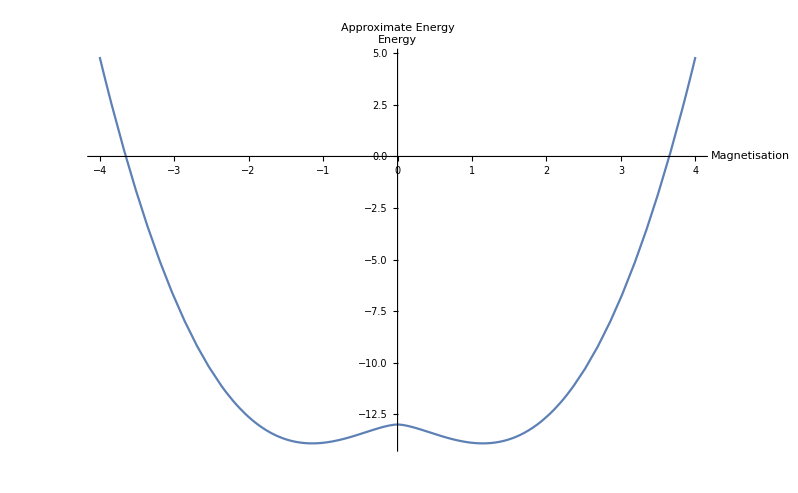

```mathematica
En[M_,R_,L_]:=M^2R-(2/L)(0.5L Sqrt[L^2+R^2M^2]+0.5R^2  M^2 ArcTanh[L/Sqrt[L^2+M^2]])
R0=4.2;
L0=13;
Plot[En[M,R0,L0],{M,-4,4},AxesLabel->{Magnetisation,Energy}, PlotLabel-> Approximate Energy]
```

## Note: this is the right shape but the scale is inconsistent due to constant pre-factor neglectations. What’s important is that the shape is captures successfully which means we can conclude that for all R>0 we have a finite magnetisation and therefore a magnetically ordered state as Jz is switched on. This means we have NO QSL in 1D.

## Excitation spectra approximation around Pi:

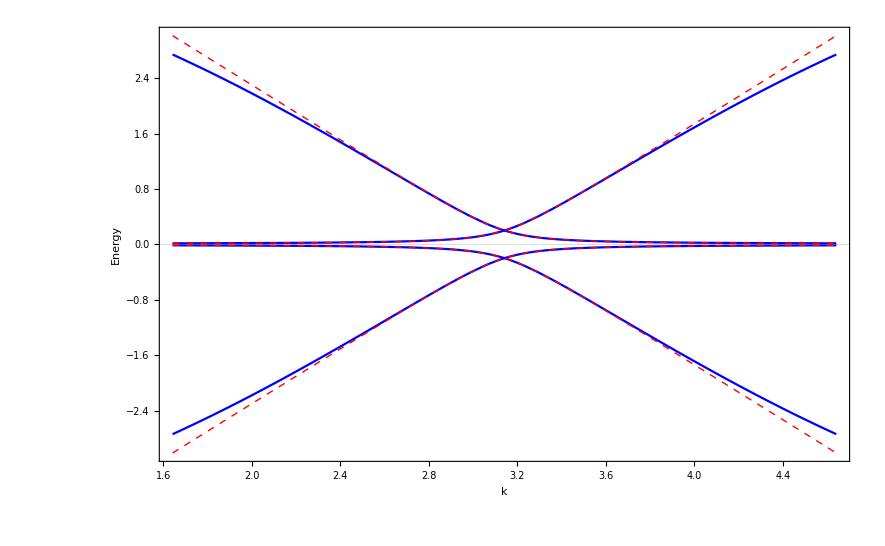

```mathematica
x=0.2;f[k_]:=2+2 Cos[k];E1[k_]:=Sqrt[2f[k]+x^2+2Sqrt[f[k]]Sqrt[f[k]+x^2]];E2[k_]:=Sqrt[2f[k]+x^2-2Sqrt[f[k]]Sqrt[f[k]+x^2]];E3[k_]:=Abs[(k-Pi)+Sqrt[((k-Pi)^2)+x^2]];E4[k_]:=Abs[(k-Pi)-Sqrt[((k-Pi)^2)+x^2]]; 
Plot[{E1[k],-E1[k],E2[k],-E2[k],E3[k],-E3[k],E4[k],-E4[k]},{k,Pi-1.5,Pi+1.5},PlotTheme->"Scientific",AxesLabel->{k,Energy},PlotStyle->{Blue,Blue,Blue,Blue,{Red,Thick,Dashed},{Red,Thick,Dashed},{Red,Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->"Solid Lines: Energy Bands
Dashed Lines: Approximate Energy Bands"]
```

# 2D Kitaev-Heisenberg Model

```mathematica
Clear[m,a,b,c,d,a0,b0,m0]
A={{m,0,c+I d,a+I b},{0,-m,-a-I b,-c-I d},{c-I d,-a+I b,-m,0},{a-I b,-c+I d,0,m}};
```

```mathematica
MatrixForm[A]
```

(m | 0 | c+ⅈ d | a+ⅈ b
0 | -m | -a-ⅈ b | -c-ⅈ d
c-ⅈ d | -a+ⅈ b | -m | 0
a-ⅈ b | -c+ⅈ d | 0 | m)

```mathematica
Eigenvalues[A]
```

{-√(a^2+b^2+c^2+d^2+m^2-2 √(a^2 c^2+2 a b c d+b^2 d^2+a^2 m^2+b^2 m^2)),√(a^2+b^2+c^2+d^2+m^2-2 √(a^2 c^2+2 a b c d+b^2 d^2+a^2 m^2+b^2 m^2)),-√(a^2+b^2+c^2+d^2+m^2+2 √(a^2 c^2+2 a b c d+b^2 d^2+a^2 m^2+b^2 m^2)),√(a^2+b^2+c^2+d^2+m^2+2 √(a^2 c^2+2 a b c d+b^2 d^2+a^2 m^2+b^2 m^2))}

```mathematica
a1={Sqrt[3]/2,3/2};a2={-Sqrt[3]/2,3/2};k={kx,ky};
2(a^2+b^2)+4+4 b(Cos[k.a1]+Cos[k.a2])+4 Cos[k.a1-k.a2]
2(a^2-b^2)+4+4 b(Cos[k.a1]+Cos[k.a2])+4 Cos[k.a1-k.a2]
```

4+2 (a^2+b^2)+4 Cos[√3 kx]+4 b (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])

4+2 (a^2-b^2)+4 Cos[√3 kx]+4 b (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])

```mathematica
eps1[kx_,ky_,a_,b_,m_]:=Sqrt[4+2 (a^2+b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+m^2+2Sqrt[(4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2/4+((a+b)^2+2+2(a+b)(Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 Cos[√3 kx])m^2]];eps2[kx_,ky_,a_,b_,m_]:=Sqrt[4+2 (a^2+b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+m^2-2Sqrt[(4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2/4+((a+b)^2+2+2(a+b)(Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 Cos[√3 kx])m^2]];
```

```mathematica
V=12Integrate[1,{kx,0,2 Pi/3/Sqrt[3]},{ky,Sqrt[3]kx,2 Pi/3}];
```

```mathematica
a0=1.0;b0=-0.5;m0=0.0;Plot3D[{eps1[kx,ky,a0,b0,m0],-eps1[kx,ky,a0,b0,m0],eps2[kx,ky,a0,b0,m0],-eps2[kx,ky,a0,b0,m0]},{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->100]
```

-Graphics3D-

```mathematica
D[eps1[kx,ky,a,b,m],m]+D[eps2[kx,ky,a,b,m],m]
```

(2 m-(2 m (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])-2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))+(2 m+(2 m (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))

```mathematica
Fa[kx_,ky_,a_,b_,m_]:=(4 a+4 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])-(m^2 (2 (a+b)+2 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))+1/2 (4 a+4 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])) (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])-2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))+(4 a+4 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+(m^2 (2 (a+b)+2 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))+1/2 (4 a+4 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])) (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))));
```

```mathematica
Fb[kx_,ky_,a_,b_,m_]:=(4 b-(m^2 (2 (a+b)+2 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))-2 b (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])-2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))+(4 b+(m^2 (2 (a+b)+2 (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))-2 b (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))));
```

```mathematica
Fm[kx_,ky_,a_,b_,m_]:=(2 m-(2 m (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])-2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))+(2 m+(2 m (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))/(√(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))))/(2 √(4+2 (a^2+b^2)+m^2+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])+2 √(1/4 (4+2 (a^2-b^2)+4 Cos[√3 kx]+4 a (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2]))^2+m^2 (2+(a+b)^2+2 Cos[√3 kx]+2 (a+b) (Cos[(√3 kx)/2-(3 ky)/2]+Cos[(√3 kx)/2+(3 ky)/2])))));
```

```mathematica
alpha=0.4256;
ap[0]=0.9;
bp[0]=-0.5;
mp[0]=0.1;
nit=50;
For[i=0,i<=nit-1,i++,bp[i+1]=-1/2 
(NIntegrate[Fa[kx,ky,ap[i],bp[i],mp[i]],{kx,-2Pi/3/Sqrt[3],2Pi/3/Sqrt[3]},{ky,-2Pi/3,2Pi/3}]+NIntegrate[Fa[kx,ky,ap[i],bp[i],mp[i]],{kx,-4Pi/3/Sqrt[3],-2Pi/3/Sqrt[3]},{ky,-Sqrt[3]kx-4Pi/3,Sqrt[3]kx +4Pi/3}]+NIntegrate[Fa[kx,ky,ap[i],bp[i],mp[i]],{kx,2Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{ky,Sqrt[3]kx-4Pi/3,-Sqrt[3]kx +4Pi/3}])/V;
ap[i+1]=-1/2 (NIntegrate[Fb[kx,ky,ap[i],bp[i],mp[i]],{kx,-2Pi/3/Sqrt[3],2Pi/3/Sqrt[3]},{ky,-2Pi/3,2Pi/3}]+NIntegrate[Fb[kx,ky,ap[i],bp[i],mp[i]],{kx,-4Pi/3/Sqrt[3],-2Pi/3/Sqrt[3]},{ky,-Sqrt[3]kx-4Pi/3,Sqrt[3]kx +4Pi/3}]+NIntegrate[Fb[kx,ky,ap[i],bp[i],mp[i]],{kx,2Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{ky,Sqrt[3]kx-4Pi/3,-Sqrt[3]kx +4Pi/3}])/V;mp[i+1]=3 alpha (NIntegrate[Fm[kx,ky,ap[i],bp[i],mp[i]],{kx,-2Pi/3/Sqrt[3],2Pi/3/Sqrt[3]},{ky,-2Pi/3,2Pi/3}]+NIntegrate[Fm[kx,ky,ap[i],bp[i],mp[i]],{kx,-4Pi/3/Sqrt[3],-2Pi/3/Sqrt[3]},{ky,-Sqrt[3]kx-4Pi/3,Sqrt[3]kx +4Pi/3}]+NIntegrate[Fm[kx,ky,ap[i],bp[i],mp[i]],{kx,2Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{ky,Sqrt[3]kx-4Pi/3,-Sqrt[3]kx +4Pi/3}])/V];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

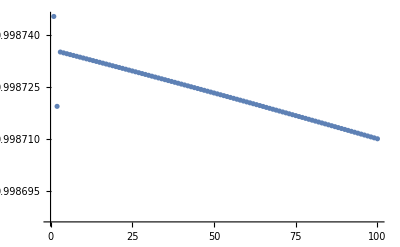

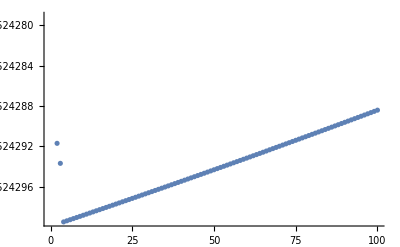

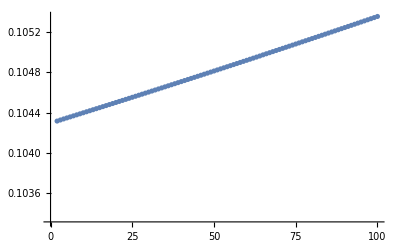

0.99871

-0.524288

0.105353

```mathematica
ListPlot[Table[{i,ap[i]},{i,0,nit}]]
ListPlot[Table[{i,bp[i]},{i,0,nit}]]
ListPlot[Table[{i,mp[i]},{i,0,nit}]]
ap[nit]
bp[nit]
mp[nit]
```

```mathematica
a0=ap[nit];b0=bp[nit];m0=mp[nit];Plot3D[{eps1[kx,ky,a0,b0,m0],-eps1[kx,ky,a0,b0,m0],eps2[kx,ky,a0,b0,m0],-eps2[kx,ky,a0,b0,m0]},{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->50]
```

-Graphics3D-